# Computer Assignment 5

## Stony Brook University, Applied Mathematics and Statistics Program in Quantitative Finance

Instructor: J.D. Pinezich

### Part A) Use the GeometricBrownianMotionProcess[] function to generate stock processes (as below in the geoBM variable). Part B) Do a sanity check on the volatility (reference: section 3.4.3 in the book). Part C) Use Monte Carlo to compute the price of a European call using risk neutral pricing. Compare your answer to that obtained using the Black-Scholes formula. Develop your solution using howManySamples = 100, but then increase to observe convergence to the Black Scholes formula value. Part D) Use Monte Carlo to compute the price of an Asian option that averages the stock price over every day up to the same expiry (see notes or section 7.5 in textbook).

### Parameters:

```mathematica
daysPerYear=252;
years=1;
howManySamples=100;
strike=90;
riskFree=.1/daysPerYear;
growthRate = .15/daysPerYear;
volatility=.02;
startPrice=100;
```

### Part A) Stock processes:

```mathematica
rate=?;
```

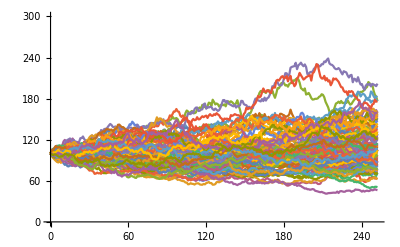

```mathematica
geoBM=Normal[RandomFunction[GeometricBrownianMotionProcess[rate,volatility,startPrice],{0,years daysPerYear,1},howManySamples]];
ListPlot[geoBM,Joined->True,PlotRange->{0,300}]
```

```mathematica
stocks=Table[Last[Transpose[geoBM⟦i⟧]],{i,howManySamples}];
```

### Part B) Sanity check the stock volatility.

### Part C)

```mathematica
payoff=Table[Last[Last[Transpose[geoBM⟦i⟧]]-strike],{i,howManySamples}];
outOfTheMoney=Flatten[Position[payoff,_?(#<0 &)]];
payoff⟦outOfTheMoney⟧=0;
payoff
```

{62.135,42.183,14.4763,11.6853,50.0844,39.3875,32.5054,31.6594,63.0041,6.64724,13.2969,0,18.2601,0,15.0117,4.36402,39.1398,29.8555,0,11.3815,22.699,47.0759,41.0458,69.6236,0,0,15.9022,0,0,0,22.1066,0,86.2348,50.412,111.923,19.7269,86.2577,19.4487,24.9631,0,3.25996,0,0,0,0,60.0922,38.5348,0,30.2292,15.0495,0,11.9129,10.9243,16.2276,8.33409,0,0,70.5409,0,0,2.80514,0,31.072,3.69301,38.4078,51.4233,92.1651,51.2523,0,0,0.016905,57.8351,49.8605,15.0994,0,0,65.0642,5.54383,45.4843,0,0.33875,0,14.7817,0,59.9701,86.3475,0,63.877,29.5411,22.9974,0,0,0,0,30.1049,19.9653,15.9193,38.7119,68.7791,31.6201}

### Part D)